```mathematica
numeraiData=Import["/home/tamellan/Desktop/Numerai/numerai_training_data.csv"];
numeraiData//Dimensions
```

{535714,54}

{{4,-0.0328565},{5,0.0146297},{6,-0.0130975},{7,-0.0288977},{8,0.0186834},{9,0.0162261},{10,0.00465576},{11,-0.0196482},{12,0.00320689},{13,-0.030519},{14,0.0115239},{15,-0.0382628},{16,-0.0120243},{17,0.00960794},{18,-0.00237087},{19,-0.004023},{20,-0.0125262},{21,-0.0101404},{22,0.0140316},{23,0.00996429},{24,-0.00840744},{25,0.00742354},{26,0.0363526},{27,0.0251093},{28,0.0121746},{29,0.0222445},{30,0.0227871},{31,-0.0095101},{32,0.0237836},{33,-0.0203385},{34,-0.0270649},{35,-0.0312809},{36,0.0188404},{37,0.00486487},{38,0.0375597},{39,0.00950368},{40,0.0207694},{41,0.0355999},{42,-0.0187051},{43,0.0178014},{44,-0.0014733},{45,-0.0119435},{46,0.00709378},{47,-0.0195449},{48,-0.013514},{49,-0.00572982},{50,0.00973585},{51,-0.00556812},{52,-0.0366302},{53,-0.0383414},{54,1}}

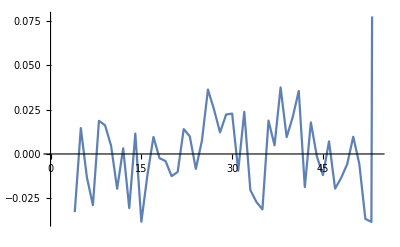

{51,50,12,35,49,23,38,1,32,10}

{{54,1},{53,-0.0383414},{15,-0.0382628},{38,0.0375597},{52,-0.0366302},{26,0.0363526},{41,0.0355999},{4,-0.0328565},{35,-0.0312809},{13,-0.030519}}

{54,53,15,38,52,26,41,4,35,13}

```mathematica
correlationTable=Table[{k,Correlation[Table[Transpose[numeraiData[[-100000;;-1]]][[i]][[2;;-1]],{i,k,k}][[1]],Table[Transpose[numeraiData[[-100000;;-1]]][[i]][[2;;-1]],{i,54,54}][[1]]]},{k,4,54}]
ListLinePlot@correlationTable
bestCorrelations=Reverse@Ordering[Abs@Transpose[correlationTable][[2]]][[-10;;-1]]
correlationTable[[bestCorrelations]]
bestCorrs=Transpose[correlationTable[[bestCorrelations]]][[1]]
```

```mathematica
trainSetSize=400000;
testSetSize=100000;
```

```mathematica
(*Select traingin and esting sets*)
topTen=Transpose[numeraiData[[-trainSetSize;;-1]]][[bestCorrs]];
topTenVal=Transpose[numeraiData[[-500;;-400]]][[bestCorrs]];
topTenTest=Transpose[numeraiData[[-(testSetSize+trainSetSize);;-trainSetSize]]][[bestCorrs]];

(*Training*)
trainInput=Transpose[topTen[[2;;-1]]];
trainOutput=topTen[[1]];
(*Validation*)
trainInputVal=Transpose[topTenVal[[2;;-1]]];
trainOutputVal=topTenVal[[1]];
(*Test*)
trainInputTest=Transpose[topTenTest[[2;;-1]]];
trainOutputTest=topTenTest[[1]];

(*Map input to output*)
f[arg_]:=arg[[1]]->arg[[2]]
trainSet=Table[f[{trainInput[[i]],trainOutput[[i]]}],{i,1,Length[trainInput]}];
trainSetTest=Table[f[{trainInputTest[[i]],trainOutputTest[[i]]}],{i,1,Length[trainInputTest]}];

(*methods={"LinearRegression","GaussianProcess","NearestNeighbors","NeuralNetwork","RandomForest"};*)
methods={"LinearRegression"};

(*Train Net*)
nets=Table[Predict[trainSet,Method->methods[[i]],PerformanceGoal->"Quality"],{i,1,Length@methods}]//AbsoluteTiming;
StringJoin[{"Timing to train net is: ",ToString@nets[[1]]," seconds"}]
net=nets[[2]];

(*Apply net to the training data*)
netTrainOutput=Table[Table[net[[j]][trainInput[[i]]],{i,1,Length@trainInput}],{j,1,Length@net}];

actualTrain=Table[{i,trainOutput[[i]]},{i,1,Length[trainInput]}];
netTrain=Table[Table[{i,netTrainOutput[[j]][[i]]},{i,1,Length[trainInput]}],{j,1,Length@net}];

(*Apply net to the testing data*)

netTrainOutputTest=Table[Table[net[[j]][trainInputTest[[i]]],{i,1,Length@trainInputTest}],{j,1,Length@net}];

actualTrainTest=Table[{i,trainOutputTest[[i]]},{i,1,Length[trainInputTest]}];
netTrainTest=Table[Table[{i,netTrainOutputTest[[j]][[i]]},{i,1,Length[trainInputTest]}],{j,1,Length@net}];

(*Analyse results*)
(*Predicted and actual results on test data*)
trueResults=Transpose[actualTrainTest][[2]];
predictedResults=Transpose[netTrainTest[[1]]][[2]];


(*Define log loss function*)
Clear[logloss]
loglossfun[binary_,prediction_]:=Table[-(binary[[i]]*Log[prediction[[i]]]+(1-binary[[i]])*Log[1-prediction[[i]]]),{i,1,Length@binary}]
(*Calculate the log loss for each time step, then find the mean*)
"The log loss is: ";
logloss=Mean@loglossfun[trueResults,predictedResults];

loglossRollingFun[binary_,prediction_]:=Table[Table[-(binary[[i]]*Log[prediction[[i]]]+(1-binary[[i]])*Log[1-prediction[[i]]]),{i,1,j}],{j,1,Length@binary}]
rollingLogLoss=Mean/@loglossRollingFun[trueResults,predictedResults];
rollingLogLossSD=StandardDeviation/@loglossRollingFun[trueResults,predictedResults][[2;;-1]];

"The log loss SD is: ";
rollingLogLossSD[[-1]];

"The log loss accuracy is: ";
rollingLogLossSD[[-1]]/Sqrt[testSetSize];

(*Define binary accuracy*)
polar2[f_]:=Table[If[f[[i]]>Mean[f],1,0],{i,1,Length@f}]
polarisedOutputTest2=Table[polar2@netTrainOutputTest[[i]],{i,1,Length[net]}];
(*Output binary accuracy - method, correlation, success*)
Table[{"Training set size is: ",trainSetSize," and testing set size is: ",testSetSize},1]//TableForm
"Method, correlation, success %, log loss, log loss accuracy"
Table[{methods[[i]],Correlation[trainOutputTest,polarisedOutputTest2[[i]]],(Correlation[trainOutputTest,polarisedOutputTest2[[i]]]+1)/2//N,logloss,rollingLogLossSD[[-1]]/Sqrt[testSetSize]},{i,1,Length@methods}]//N//TableForm
```

Timing to train net is: 0.652593 seconds

Training set size is:  | 100000 |  and testing set size is:  | 10000

Method, correlation, success %, log loss, log loss accuracy

LinearRegression | 0.0176855 | 0.508843 | 0.693163 | 0.000558918

```mathematica
(*Visualisations*)
p1=ListLinePlot[{rollingLogLoss,Table[logloss,Length@rollingLogLoss]},PlotRange->{Automatic,{0.683,0.72}},PlotLegends->{"Logloss convergence","Logloss"},FrameLabel->{"datapoint","logloss"},Frame->True,ImageSize->500];
p2=ListLinePlot[Table[rollingLogLossSD[[i]]/Sqrt[i],{i,1,Length@rollingLogLossSD-1}],PlotLegends->{"sd/Sqrt[i]"},FrameLabel->{"datapoint","accuracy"},Frame->True,ImageSize->500];
GraphicsGrid[{{p1,p2}},ImageSize->{1300,740},Spacings->0]
```

-Graphics-

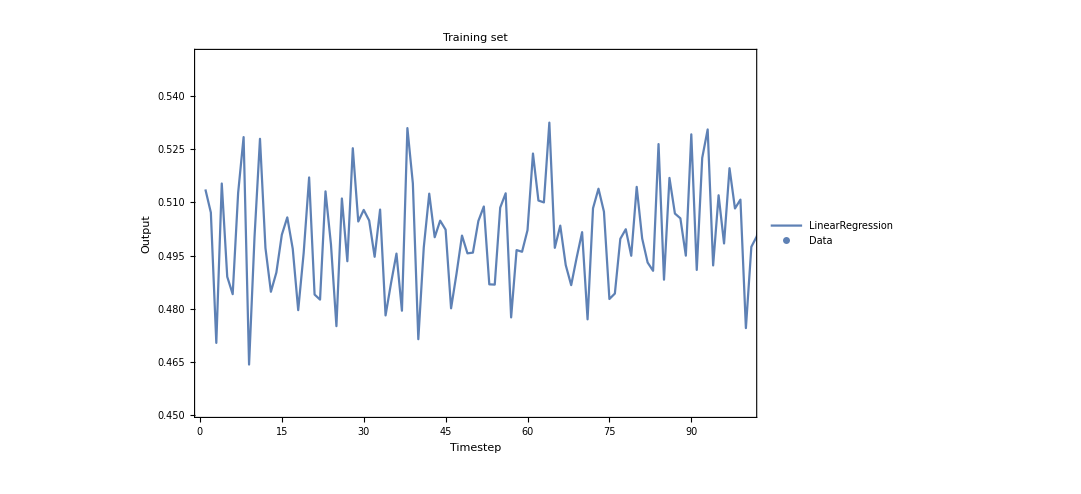

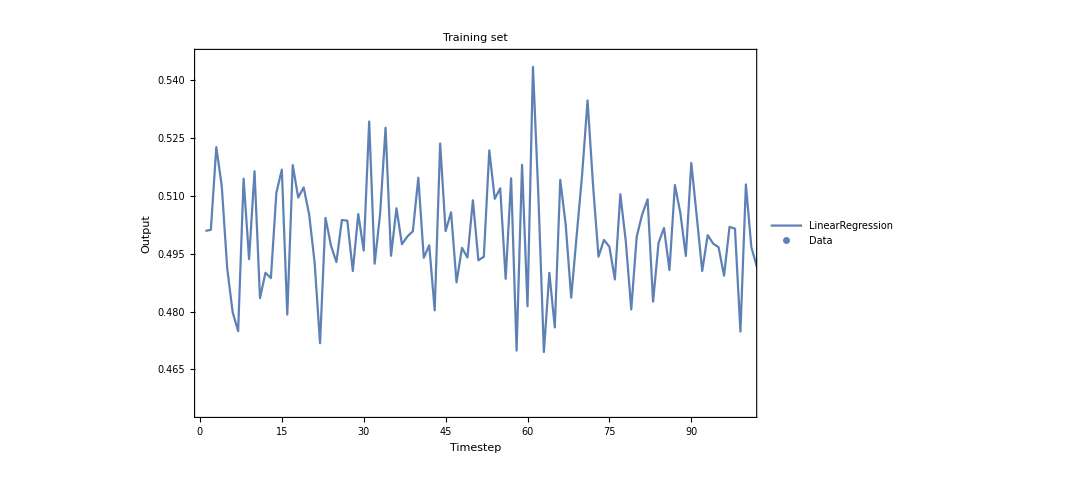

```mathematica
style[arg_]:=Table[Style[arg[[i]],16,Black],{i,1,Length@arg}]
plotOpts={PlotLegends->Placed[style[methods],{0.15,0.28}],Frame->True,FrameLabel->{Style["Timestep",18,Black],Style["Output",18,Black]},FrameStyle->Directive[Thickness[0.004],Black],ImageSize->800,FrameTicksStyle->18,PlotRange->{{1,100},Automatic}};Show[{ListLinePlot[netTrain,Evaluate@plotOpts,PlotLabel->Style["Training set",Black,18]],ListPlot[actualTrain,PlotLegends->Placed[{Style["Data",16,Black]},{0.45,0.85}]]}]
Show[{ListLinePlot[netTrainTest,Evaluate@plotOpts,PlotLabel->Style["Training set",Black,18]],ListPlot[actualTrainTest,PlotLegends->Placed[{Style["Data",16,Black]},{0.45,0.85}]]}]
```

```mathematica
(*2000training, 2000testing - {{"LinearRegression", 0.1005278214652477, 0.5502639107326238, 0.6867619038430586, 0.001888464122952996}}*)

(*"<Training set size is: > | 20000 | < and testing set size is: > | 2000"
"0.100528 | 0.550264 | 0.686762 | 0.00188846"*)

(*"<Training set size is: > | 20000 | < and testing set size is: > | 2000"
"<LinearRegression> | 0.0395861 | 0.519793 | 0.691382 | 0.000659451"*)

(*{{"Training set size is: ", 50000, " and testing set size is: ", 2000}}
{{"LinearRegression", 0.06279176276996125, 0.5313958813849806, 0.6914105407186204, 0.000617750029293622}}*)

(*
{{"Training set size is: ", 100000, " and testing set size is: ", 2000}}
{{"LinearRegression", 0.06058740727249449, 0.5302937036362473, 0.6914962253481756, 0.0012635619913129708}}
*)

(*
{{"Training set size is: ", 100000, " and testing set size is: ", 10000}}
{{"LinearRegression", 0.017685491864945474, 0.5088427459324727, 0.6931632842153858, 0.000558918026093522}}
*)
```